```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Limit[k*ExpIntegralE[k+1,k*A*(d-1)],d->1,Assumptions->{k>3/2,A>0}]
Limit[k*Exp[k*A*(d-1)]ExpIntegralE[k+1,k*A*(d-1)],d->Infinity,Assumptions->{k>3/2,A>0}]
```

1

0

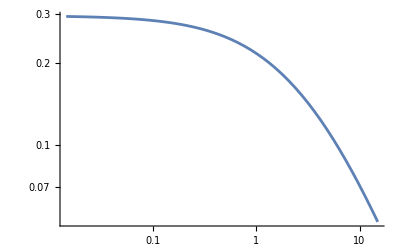

0.0521897

0.0472444

0.0526956

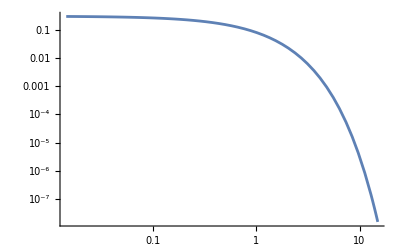

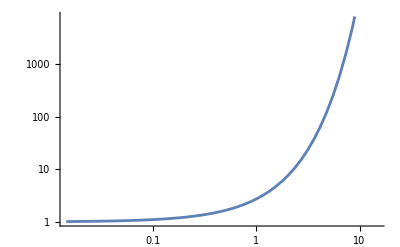

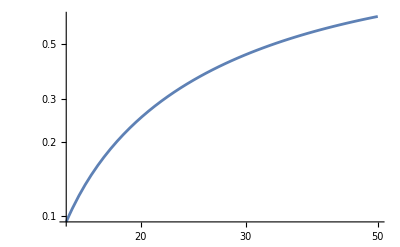

```mathematica
LogLogPlot[Exp[x]*ExpIntegralE[3.37+1,x],{x,0,15}]
Exp[15]*ExpIntegralE[3.37+1,15]
g2[x_,κ_]=1/x+(-1-κ)/x^2;
g5[x_,κ_]=1/x+(-1-κ) (1/x)^2+(1+κ) (2+κ) (1/x)^3-(1+κ) (2+κ) (3+κ) (1/x)^4+(1+κ) (2+κ) (3+κ) (4+κ) (1/x)^5;
g2[15,3.37]
g5[15,3.37]
LogLogPlot[ExpIntegralE[3.37+1,x],{x,0,15}]
LogLogPlot[Exp[x],{x,0,15}]

LogLogPlot[(Exp[15]*ExpIntegralE[3.37+1,15] - g2[x,3.37])/(Exp[15]*ExpIntegralE[3.37+1,15]),{x,15,50}]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Limit[k*Exp[x]*ExpIntegralE[k+1,x],x->Infinity,Assumptions->{k>3/2}]
FullSimplify[Series[κ*Exp[1/y]*ExpIntegralE[κ+1,1/y],{y,0,2},Assumptions->κ>3/2],{κ>3/2,y∈Reals}]

FullSimplify[Series[Exp[1/y]*ExpIntegralE[κ+1,1/y],{y,0,2},Assumptions->κ>3/2],{κ>3/2,y∈Reals}]
```

0

κ y-κ (1+κ) y^2+O[y]^3

y+(-1-κ) y^2+O[y]^3

```mathematica
y=1/x;
κ y-κ (1+κ) y^2
```

κ/x-(κ (1+κ))/x^2

1543.46

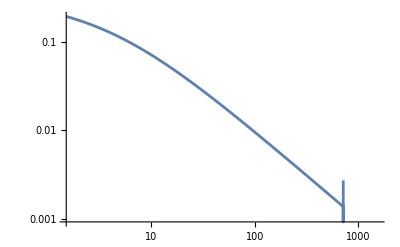

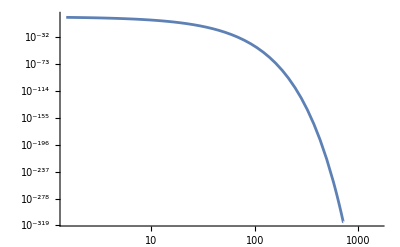

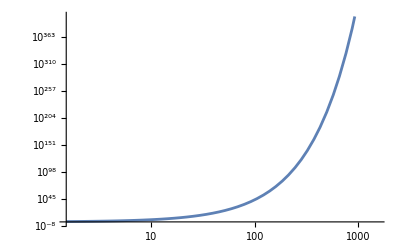

```mathematica
xf=458*3.37
LogLogPlot[Exp[x]*ExpIntegralE[3.37+1,x],{x,0,xf}]
LogLogPlot[ExpIntegralE[3.37+1,x],{x,0,xf}]
LogLogPlot[Exp[x],{x,0,xf}]
```

```mathematica
(1/15.)^4
```

0.0000197531

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Limit[k*ExpIntegralE[k+1,k*A*(d-1)],d->1,Assumptions->{k>3/2,A>0}]
Limit[k*Exp[k*A*(d-1)]ExpIntegralE[k+1,k*A*(d-1)],d->Infinity,Assumptions->{k>3/2,A>0}]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
Limit[k*Exp[x]*ExpIntegralE[k+1,x],x->0,Assumptions->{k>2/2}]
FullSimplify[Series[κ*Exp[x]*ExpIntegralE[κ+1,x],{x,0,2},Assumptions->κ>2/2],{κ>2/2,x∈Reals}]

FullSimplify[Series[Exp[x]*ExpIntegralE[κ+1,x],{x,0,2},Assumptions->κ>2/2],{κ>2/2,x∈Reals}]
```

1

(1+x/(1-κ)+x^2/(2-3 κ+κ^2)+O[x]^3)+x^κ (κ Gamma[-κ]+κ Gamma[-κ] x+1/2 κ Gamma[-κ] x^2+O[x]^3)

(1/κ+x/(κ-κ^2)+x^2/(2 κ-3 κ^2+κ^3)+O[x]^3)+x^κ (Gamma[-κ]+Gamma[-κ] x+1/2 Gamma[-κ] x^2+O[x]^3)

```mathematica
Plot[{(1+x/(1-κ)+x^2/(2-3 κ+κ^2))/(κ*Exp[x]*ExpIntegralE[κ+1,x]),},{x,0,2},PlotLegends->"Expressions",Frame->True,FrameLabel->{"x","approx"}]
```

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]
FullSimplify[Series[κ*Exp[κ*x]*ExpIntegralE[κ+1,κ*x],{x,0,1},Assumptions->κ>2/2],{κ>2/2,x∈Reals}]
```

(1-(κ x)/(-1+κ)+O[x]^2)+x^κ (κ^(1+κ) Gamma[-κ]+κ^(2+κ) Gamma[-κ] x+O[x]^2)

```mathematica
f[x_,κ_]:=(1-(κ x)/(-1+κ)+x^κ *(κ^(1+κ) Gamma[-κ]+κ^(2+κ) Gamma[-κ] x))/(κ*Exp[κ*x]*ExpIntegralE[κ+1,κ*x]);

Plot[{f[x,κ1],f[x,κ2],f[x,κ3],f[x,κ4]},{x,0,2},PlotLegends->{"κ=","κ=","κ=","κ="},Frame->True,FrameLabel->{"x=A_0(B_0/B-1)","approx/Exact"}]
```